# Calculating The Geometric Mean Over Continuous Distributions

Let f(x) denote a probability density function, then we can calculate the geometric mean as follows:

G:=e^(∫Ln[f(x)]ⅆx)

or equivalently

Log[G]:=∫Ln[f(x)]ⅆx

### The Geometric Mean of a Linear Distribution

If f(x) is a line, then we can calculate the geometric mean as follows:

Log[G]:=∫_a^b Log[(p_b-p_a)/(b-a)(x-a)+p_a]ⅆx

Where a, b, p_a and p_b are as seen on the following graphic,

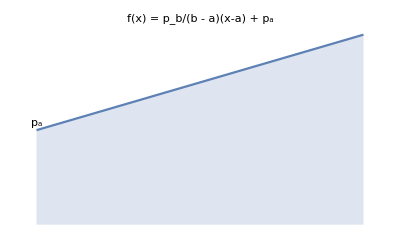

```mathematica
Show[
Plot[
1.01x+1,
{x,0,1},
Filling->Bottom,
AxesOrigin->{0,0},
Axes->False,
PlotLabel->"f(x) = p_b/(b - a)(x-a) + p_a"
],
Graphics[Text["a",{0,0-0.05}]],
Graphics[Text["b",{1,0-0.05}]],
Graphics[Text["p_a",{0,1.08}]],
Graphics[Text["p_b",{1,2.08}]]
]
```

The integral can be solved analytically, yielding the following equation:

Log[G]:=(a-b)  (Log[p_a^p_a p_b^-p_b] + p_b- p_a)/(p_b - p_a)

```mathematica
(*
Integrate[
Log[(pb-pa)/(b-a)*(x-a)+pa],
{x,a,b},
Assumptions->{
Element[d|a|b|pa|pb,Reals],
0 < a < b, 
0 ≤ pa < pb ≤ 1}
]
*)
```